```mathematica
Integrate[-x Exp[-x],x]
```

-ⅇ^-x (-1-x)

```mathematica
Clear[ω]
```

```mathematica
D[Exp[-r^2/ω^2],r]
```

-(2 ⅇ^(-r^2/ω^2) r)/ω^2

```mathematica
ω??
```

Information::basic: ?Name gives information on Name, ?Ab* on all symbols starting with Ab. ??Name gives more information.

0.0002

```mathematica
Integrate[Exp[-r^2/ω^2]Exp[-r/a],{r,0,∞}]
```

ConditionalExpression[1/2 ⅇ^(ω^2/(4 a^2)) √π ω (-1+√(1/ω^2) ω+Erfc[ω/(2 a)]),Re[ω^2]>0||(Re[ω^2]≥0&&Re[a]>0)]

```mathematica
Integrate[(1-Exp[-(1+Cos[x])*a])/((1+Cos[x])*a),{x,0,π}]
```

ConditionalExpression[ⅇ^-a π (BesselI[0,a]+BesselI[1,a]),Re[a]>0]

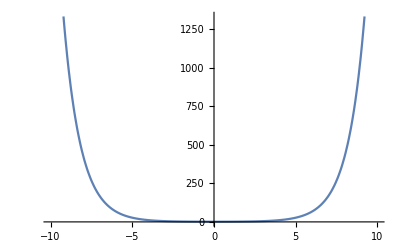

```mathematica
Plot[BesselI[0,x],{x,-10,10}]
```

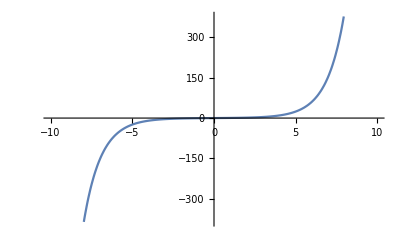

```mathematica
Plot[BesselI[1,x],{x,-10,10}]
```

Bessel function tests, plotting Bessel functions:

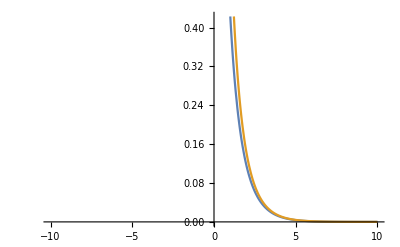

```mathematica
Plot[{BesselK[0,x],BesselK[1,x]},{x,-10,10}]
```

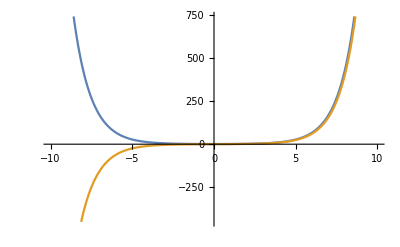

```mathematica
Plot[{BesselI[0,x],BesselI[1,x]},{x,-10,10}]
```

```mathematica
BesselK[0,1]
```

BesselK[0,1]

```mathematica
N[BesselK[0,1]]
```

0.421024